# The Simulation of Gravitational N-Body Problem

Yousef Sadeghi, Arash T. Jamshidi
Department of Physics, Faculty of Science, Ferdowsi University of Mashhad

Abstract

This paper will present the results and analysis of N-Body simulation. We use Mathematica to simulate the motion of objects. Our goal is to accurately simulate orbits of the Solar System. We find the perihelion advance of planets with an emphasis on planet Mercury considering Newtonian and Relativistic effects.

Keywords

Mercury, N-Body, Gravity, Newtonian, Relativity, Mechanics, Perihelion Advance, Precession

1. Introduction
The N-Body problem is the problem of predicting the individual motions of a group of celestial objects interacting with each other gravitationally. Solving this problem has been motivated by the desire to understand the motions of the Sun, Moon, planets, and visible stars.
The classical physical problem can be informally stated as the following:
“Given the quasi-steady orbital properties (instantaneous position, velocity and time)[3] of a group of celestial bodies, predict their interactive forces; and consequently, predict their true orbital motions for all future times.”
The two-body problem has been completely solved and is discussed below, as well as the famous restricted three-body problem.
The problem of finding the general solution of the n-body problem was considered very important and challenging. Indeed, in the late 19th century King Oscar II of Sweden, advised by Gösta Mittag-Leffler, established a prize for anyone who could find the solution to the problem.
The n-body problem in general relativity is considerably more difficult to solve due to additional factors like time and space distortions.
In this paper we simulate the n-body system using Mathematica by solving differential equations of motion directly and numerically using NDSolve after which we use Animate to show the motion of each body.
Using the same method we simulate the motion of Solar System planets from Mercury to Neptune. In such a system gravitational tugs of planets would cause a precession in orbital movement. The most effected planet is Mercury with a precession of 574.10 (arcsec/century). We will try to calculate the precession of each planet using different methods.

2. Materials and Methods

2.1. Experimental Tools
We used Mathematica to do the calculation and draw graph to simulate N-Body.

2.2. The Initial Data
In order to simulate the revolution orbit of planets, we need initial data, the data is listed:
1) The mass, semimajor axis, perihelion, eccentricity and period are displayed in Table 1.

Table 1. Mass, semimajor axis, perihelion, eccentricity and period in days.

| Mercury | Venus | Earth | Mars | Jupiter | Saturn | Uranus | Neptune
Mass(kg) *10^24 | 0.33010 | 4.8673 | 5.9722 | 0.64169 | 1898.1 | 568.32 | 86.81 | 102.41
Semimajor Axis(m) *10^11 | 0.57909227 | 1.0820948 | 1.4959826 | 2.2794382 | 7.7834082 | 14.266664 | 28.706582 | 44.983964
Perihelion(m) *10^11 | 0.46 | 1.07476 | 1.47098 | 2.06655 | 7.40680 | 13.4982 | 27.35 | 44.5975
Eccentricity | 0.20563593 | 0.00677672 | 0.01671123 | 0.0933941 | 0.04838624 | 0.05386179 | 0.04725744 | 0.00859048
Period(day) | 87.97 | 224.70 | 365.26 | 686.98 | 4332.82 | 10755.70 | 30687.15 | 60190.03
Average Orbital Speed (km/s) | 47.36 | 35.02 | 29.78 | 24.007 | 13.07 | 9.68 | 6.8 | 5.43

2) G = Gravity constant = 6.673 × 10^-11(N.m^2 .kg^-2)
3) Mass of Sun = 1.9891 × 10^30 (kg)

2.3. Depending Theory
Law of universal gravitation
Newton's second law 
F⃗ = m r^OverVector[..]
Law of conservation of energy
The total energy of an isolated system remains constant.
E_initial = E_1 = E_2 = E_3 = ... = E_n
Law of conservation of angular momentum
The total angular momentum of a system remains constant unless acted on by an external torque.
X,Y components
We separated the x component and y component of Force, speed, acceleration.

2.3.1. Two-Body

Let (r⃗)_1 and (r⃗)_2 be the vector position of two bodies and  m_1 and m_2 their masses , the goal is to determine the trajectories r_1(t) and r_2(t) for all times “t”, given initial positions x(0) and y(0) and initial velocities x'(0) and y'(0)
Piecewise[{{f_12=, m_1 OverDoubleDot[r_1]}, {f_21=, m_2 OverDoubleDot[r_2]}}]→Piecewise[{{m_1 (ⅆ^2 r_1)/(ⅆ t^2)=, (m_1 m_2 G)/(|OverVector[r_2]-OverVector[r_1]|)^2 OverHat[|OverVector[r_2]-OverVector[r_1]|]}, {m_2 (ⅆ^2 r_2)/(ⅆ t^2)=, -(m_1 m_2 G)/(|OverVector[r_2]-OverVector[r_1]|)^2 OverHat[|OverVector[r_2]-OverVector[r_1]|]}}]
at first we transfer the origin of the coordinates to the center of mass so we have:

R⃗=(m_1(r⃗)_1+m_2(r⃗)_2)/(m_1+m_2)⟶R⃗=0⟹m_1(r⃗)_1+m_2(r⃗)_2=0
r⃗=OverVector[r_2]-OverVector[r_1]⟶Piecewise[{{(r⃗)_1=, m_2/(m_1+m_2)r⃗}, {OverVector[r_2]=, -m_1/(m_1+m_2)r⃗}}]
⟹Piecewise[{{m_1 ⅆ^2/(ⅆ t^2)(m_2/(m_1+m_2)r⃗)=, (m_1 m_2 G)/(|OverVector[r_2]-OverVector[r_1]|)^2 OverHat[|OverVector[r_2]-OverVector[r_1]|]}, {m_2 ⅆ^2/(ⅆ t^2)(-m_1/(m_1+m_2)r⃗)=, (m_1 m_2 G)/(|OverVector[r_2]-OverVector[r_1]|)^2 OverHat[|OverVector[r_2]-OverVector[r_1]|]}}]⟶ξ =(m_1 m_2)/(m_1+m_2)

⟹ξ(ⅆ^2 r)/(ⅆ t^2)= ((m_1+m_2)ξ G)/(|OverVector[r_2]-OverVector[r_1]|)^2 OverHat[|OverVector[r_2]-OverVector[r_1]|]
This differential equation leads to the equation of path, which is equivalent to the equation of motion in which a particle of mass ξ moves around a particle of mass (m_1+m_2)

2.3.2. General Relativity effect
TBD

3. Simulating Gravitational Environment

3.1 Modeling Gravitational Effect
We calculate the gravitational forces between n particles, The gravitational force between two masses is given by:
F⃗ = (M m G)/(|OverVector[r_2]-OverVector[r_1]|)^2 OverHat[|OverVector[r_2]-OverVector[r_1]|]
According to the Newton’s second law, we obtain the acceleration:
r^OverVector[..] = (M G)/(|OverVector[r_2]-OverVector[r_1]|)^2 OverHat[|OverVector[r_2]-OverVector[r_1]|]
and since the Newton’s gravitational force is a linear system, we can use the superposition principle to add up multiple accelerations together.
The program first creates the differential equation of motion for each object then solves them numerically using the given initial conditions and simulates them using Animate.

```mathematica
n=7;G=1;tm=10;(*number of objects, Gravitational constant, time frame*)
m={2,5,7,6,14,7,5};(*mass of objects*)
Subscript[r, 0]={{1,0,0},{-1,0,0},{2,0,0},{2,4,0},{4,1,0},{0,4,2},{0,6,2}};(*initial coordinates*)
Subscript[r', 0]={{0,-0.7,0},{0,0.3,0},{0,0.1,0},{0.2,0,0},{0.4,0,0},{0,0,0.2},{0,0,-0.2}};(*initial velocity*)
r[t_]=Table[{Subscript[x, i][t],Subscript[y, i][t],Subscript[z, i][t]},{i,n}];(*position vector*)
fg:=(G*m[[j]]*(r[t][[j]]-r[t][[i]]))/(Norm[r[t][[j]]-r[t][[i]]])^3(*gravitational force*)
deq=Table[D[r[t][[i]], {t,2}]==∑_(j=1)^(i-1) fg+∑_(j=i+1)^n fg,{i,n}];
```

3.2. Solving for Equations of Motion

```mathematica
lr=Flatten[Table[{Subscript[x, i],Subscript[y, i],Subscript[z, i]},{i,n}]];
bv=Flatten[Table[Thread[Table[{r[0][[i1]]==Subscript[r, 0][[i1]],r'[0][[i1]]==Subscript[r', 0][[i1]]},{i1,n}][[i2]][[j]]],{i2,n},{j,2}]];
var=lr/.NDSolve[{Flatten[Table[Thread[deq[[i]]],{i,n}]],bv},lr,{t,0,tm}][[1]];
```

3.3. Simulating N-Body

```mathematica
Animate[Show[ParametricPlot3D[Evaluate[Table[{var[[i]][t1],var[[i+1]][t1],var[[i+2]][t1]},{i,1,3*n,3}]],{t1,0.01,t}],
Graphics3D[{PointSize->Medium,Point[Table[{var[[i]][t],var[[i+1]][t],var[[i+2]][t]},{i,1,3*n,3}]]}],PlotRange->Automatic],
{t,0,tm},AnimationRate->1,AnimationRunning->False]
```

4. Simulating the Solar System
Simulating with real values takes a lot of time so for the sake of brevity 1 unit of mass is mass of Earth ,1 unit of distance is 1 astronomical unit and big G is 1, consequently velocity is multiplied by a factor β shown below.

4.1. Modeling the Revolution Orbit of Planets

```mathematica
n=9;G=1;tm=1;β=19.5342;(*number of objects, Gravitational constant, time frame, scale factor of velocity × 10^3*)
m={332950,0.055,0.815,1,0.107,317.8,95.159,14.536,17.147};(*mass of planets proportion to mass of earth*)
Subscript[r, 0]={{0,0,0},{0.466697,0,0},{0.728213,0,0},{1,0,0},{1.666,0,0},{5.4588,0,0},{10.1238,0,0},{20.0965,0,0},{30.33,0,0}};(*distance from the sun in astronomical units*)
Subscript[r', 0]={{0,0,0},{0,β*47.36,0},{0,β*35.02,0},{0,β*29.78,0},{0,β*24.007,0},{0,β*13.07,0},{0,β*9.68,0},{0,β*6.8,0},{0,β*5.43,0}};(*velocity around the sun*)
r[t_]=Table[{Subscript[x, i][t],Subscript[y, i][t],Subscript[z, i][t]},{i,n}];(*position vector*)
fg:=(G*m[[j]]*(r[t][[j]]-r[t][[i]]))/(Norm[r[t][[j]]-r[t][[i]]])^3(*gravitational force*)
deq=ReplacePart[Table[D[r[t][[i]], {t,2}]==∑_(j=1)^(i-1) fg+∑_(j=i+1)^n fg,{i,n}],1->D[r[t][[1]], {t,2}]==0];
```

```mathematica
lr=Flatten[Table[{Subscript[x, i],Subscript[y, i],Subscript[z, i]},{i,n}]];
bv=Flatten[Table[Thread[Table[{r[0][[i]]==Subscript[r, 0][[i]],r'[0][[i]]==Subscript[r', 0][[i]]},{i,n}][[i]][[j]]],{i,n},{j,2}]];
var=lr/.NDSolve[{Flatten[Table[Thread[deq[[i]]],{i,n}]],bv},lr,{t,0,tm}][[1]];
```

```mathematica
Animate[Show[ParametricPlot3D[Evaluate[Table[{var[[i]][t1],var[[i+1]][t1],var[[i+2]][t1]},{i,1,3*n,3}]],{t1,10^-10,t}],
Graphics3D[{PointSize->Medium,Point[Table[{var[[i]][t],var[[i+1]][t],var[[i+2]][t]},{i,1,3*n,3}]]}],PlotRange->Automatic],{t,0,tm},AnimationRate->0.01,AnimationRunning->False]
```

```mathematica
n=9;G=1;tm=1;β=19.5342;(*number of objects, Gravitational constant, time frame, scale factor of velocity × 10^3*)
m={332950,0.055,0.815,1,0.107,317.8,95.159,14.536,17.147};(*mass of planets proportion to mass of earth*)
Subscript[r, 0]={{0,0},{0.466697,0},{0.728213,0},{1,0},{1.666,0},{5.4588,0},{10.1238,0},{20.0965,0},{30.33,0}};(*distance from the sun in astronomical units*)
Subscript[r', 0]={{0,0},{0,β*47.36},{0,β*35.02},{0,β*29.78},{0,β*24.007},{0,β*13.07},{0,β*9.68},{0,β*6.8},{0,β*5.43}};(*velocity around the sun*)
r[t_]=Table[{Subscript[x, i][t],Subscript[y, i][t]},{i,n}];(*position vector*)
fg:=(G*m[[j]]*(r[t][[j]]-r[t][[i]]))/(Norm[r[t][[j]]-r[t][[i]]])^3(*gravitational force*)
deq=ReplacePart[Table[D[r[t][[i]], {t,2}]==∑_(j=1)^(i-1) fg+∑_(j=i+1)^n fg,{i,n}],1->D[r[t][[1]], {t,2}]==0];
```

```mathematica
lr=Flatten[Table[{Subscript[x, i],Subscript[y, i]},{i,n}]];
bv=Flatten[Table[Thread[Table[{r[0][[i]]==Subscript[r, 0][[i]],r'[0][[i]]==Subscript[r', 0][[i]]},{i,n}][[i]][[j]]],{i,n},{j,2}]];
var=lr/.NDSolve[{Flatten[Table[Thread[deq[[i]]],{i,n}]],bv},lr,{t,0,tm}][[1]];
```

```mathematica
Timing[lst=Table[Show[ParametricPlot[Evaluate[Table[{var[[i]][t1],var[[i+1]][t1]},{i,1,2*n,2}]],{t1,10^-10,t}],
Graphics[{PointSize->Medium,Point[Table[{var[[i]][t],var[[i+1]][t]},{i,1,2*n,2}]]}],PlotRange->All],{t,0,tm,10^-4}]]
```

4.2. Modeling Mercury’s Perihelion Advance
In 1846, famed astronomer Urbain Le Verrier embarked on a study of the planets in the outer solar system after that he turned his attention to the inner solar system and to a study of Mercury. 
Mercury was noted to have a strong elliptical orbit, at least in comparison to other planets.  It had also been noted that its orbit rotated as a whole, such that its closest point to the Sun “the perihelion” was seen to steadily advance over a period of years.  The reason for this was assumed to be that the outer planets’ gravity was pulling Mercury’s orbit around. By undertaking an onerous effort of detailed hand-calculations he determined that the outer planets should cause Mercury’s perihelion to advance by 527 arcseconds per century. Le Verrier determined its actual advance, based on observations spanning a century and a half, was 565 arcseconds/century.  This left a discrepancy of 38 arcs/century that could not be accounted for by Newtonian gravity. Using better observational data and improved calculations, the 38 discrepancy has since been revised to 43 arcs/century and the accepted explanation for it is that it is fully due to the predictions of General Relativity.

4.2.1. Newtonian Mechanics

```mathematica
name={"Mercury","Venus","Earth","Mars","Jupiter","Saturn","Uranus","Neptune"};
m={3.3010*10^23,4.8673*10^24,5.9722*10^24,6.4169*10^23,1.8981*10^27,5.6832*10^26,8.6810*10^25,1.0241*10^26};
a={5.7909227*10^10,1.0820948*10^11,1.4959826*10^11,2.2794382*10^11,7.7834082*10^11,1.4266664*10^12,2.8706582*10^12,4.4983964*10^12};
G=6.67*10^-11;M_☉=1.9891*10^30;sum=0;l={};
f0=-(G *π *M_☉* m[[1]])/a[[1]]^2;
For[i1=2,i1<=8,i1++,
fa=G *π* m[[1]](m[[i1]]* a[[1]])/(2*π *a[[i1]](a[[i1]]^2-a[[1]]^2));
fda=G* π*m[[1]]* a[[1]]* (m[[i1]]*(a[[i1]]^2+a[[1]]^2))/(2*π *a[[i1]]*(a[[i1]]^2-a[[1]]^2)^2);
ψ=π/(√(3+(-2 *f0+fda)/(f0+fa)))-π;
arcsec=(2π(1+ψ)-2π)(180/π ) *3600*(100*365.26/87.97);
AppendTo[l,{name[[i1]],arcsec}];
sum+=arcsec];
Grid[AppendTo[l,{"total",sum}],Frame->All]
```

"Venus" | 268.857
"Earth" | 92.3903
"Mars" | 2.38709
"Jupiter" | 160.085
"Saturn" | 7.73285
"Uranus" | 0.144691
"Neptune" | 0.0443413
"Total" | 531.641

```mathematica
n=3;G=1;tm=5;β=19.5342;
m={1000,1,15};
Subscript[r, 0]={{0,0,0},{2,0,0},{5,0,0}};
Subscript[r', 0]={{0,0,0},{0,25,0},{0,15,0}};
r[t_]=Table[{Subscript[x, i][t],Subscript[y, i][t],Subscript[z, i][t]},{i,n}];
fg:=(G*m[[j]]*(r[t][[j]]-r[t][[i]]))/(Norm[r[t][[j]]-r[t][[i]]])^3
deq=ReplacePart[Table[D[r[t][[i]], {t,2}]==∑_(j=1)^(i-1) fg+∑_(j=i+1)^n fg,{i,n}],1->D[r[t][[1]], {t,2}]==0];
```

```mathematica
lr=Flatten[Table[{Subscript[x, i],Subscript[y, i],Subscript[z, i]},{i,n}]];
bv=Flatten[Table[Thread[Table[{r[0][[i]]==Subscript[r, 0][[i]],r'[0][[i]]==Subscript[r', 0][[i]]},{i,n}][[i]][[j]]],{i,n},{j,2}]];
var=lr/.NDSolve[{Flatten[Table[Thread[deq[[i]]],{i,n}]],bv},lr,{t,0,tm}][[1]];
```

```mathematica
ParametricPlot3D[Evaluate[Table[{var[[i]][t1],var[[i+1]][t1],var[[i+2]][t1]},{i,1,3*n,3}]],{t1,10^-10,tm},PlotPoints->100000,PlotStyle->Thin]
```

```mathematica
Show[ParametricPlot3D[{var[[4]][t1],var[[5]][t1],var[[6]][t1]},{t1,10^-10,1},PlotPoints->100000,PlotStyle->{Thin,Blue}],ParametricPlot3D[{var[[4]][t1],var[[5]][t1],var[[6]][t1]},{t1,4,5},PlotPoints->100000,PlotStyle->{Thin,Red}]]
```

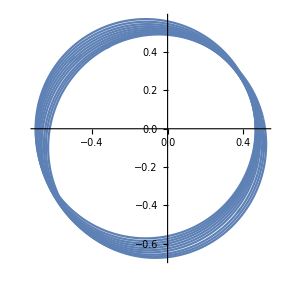
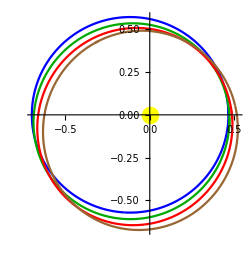
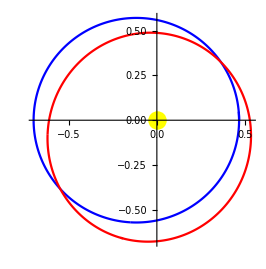
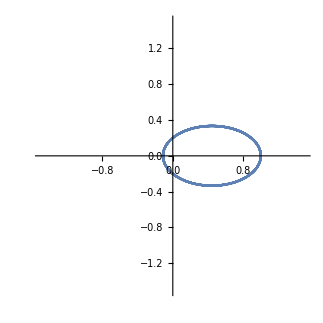
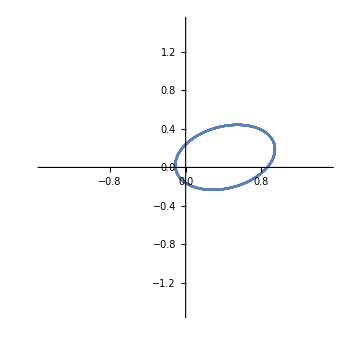
-Graphics--Graphics--Graphics-
-Graphics3D-
-Graphics--Graphics-

4.2.2. General Relativity Effect

```mathematica
n=2;G=1;tm=100;β=19.5342;a=10000;
m={10000,1};
Subscript[r, 0]={{0,0,0},{30,0,0}};
Subscript[r', 0]={{0,0,0},{0,12,0}};
r[t_]=Table[{Subscript[x, i][t],Subscript[y, i][t],Subscript[z, i][t]},{i,n}];
fg:=(G*m[[j]]*(r[t][[j]]-r[t][[i]]))/(Norm[r[t][[j]]-r[t][[i]]])^3+(a*(r[t][[j]]-r[t][[i]]))/(Norm[r[t][[j]]-r[t][[i]]])^5
deq=ReplacePart[Table[D[r[t][[i]], {t,2}]==∑_(j=1)^(i-1) fg+∑_(j=i+1)^n fg,{i,n}],1->D[r[t][[1]], {t,2}]==0];
```

```mathematica
lr=Flatten[Table[{Subscript[x, i],Subscript[y, i],Subscript[z, i]},{i,n}]];
bv=Flatten[Table[Thread[Table[{r[0][[i]]==Subscript[r, 0][[i]],r'[0][[i]]==Subscript[r', 0][[i]]},{i,n}][[i]][[j]]],{i,n},{j,2}]];
var=lr/.NDSolve[{Flatten[Table[Thread[deq[[i]]],{i,n}]],bv},lr,{t,0,tm}][[1]];
```

```mathematica
Animate[Show[ParametricPlot3D[Evaluate[Table[{var[[i]][t1],var[[i+1]][t1],var[[i+2]][t1]},{i,1,3*n,3}]],{t1,10^-10,t}],
Graphics3D[{PointSize->Medium,Point[Table[{var[[i]][t],var[[i+1]][t],var[[i+2]][t]},{i,1,3*n,3}]]}],PlotRange->All],{t,0,tm},AnimationRate->1,AnimationRunning->False]
```

```mathematica
ParametricPlot3D[Evaluate[Table[{var[[i]][t1],var[[i+1]][t1],var[[i+2]][t1]},{i,1,3*n,3}]],{t1,10^-10,tm},PlotPoints->100000]
```

-Graphics3D-

5. Conclusions
By modeling the Solar System we saw gravitational tugs of planets and relativistic effects on orbital movement, using the ring method we calculated a 531.641289925 arcs/century precession for Mercury.
Early analysis of Mercury’s motion was based on simplified models that ignored aspects such as the outer planets’ speeds, their combined contributions, and the motion of the Sun.  This led to the conclusion that Newtonian gravity would predict Mercury to precess by 532 arcseconds per century, and that there exists a discrepancy of 43 arcs/cent that can be attributed to General Relativity.

Acknowledgements
We would like to thank our supervisor, Professor Mahmood Roshan, a famous professor from Ferdowsi University of Mashhad who has provided us with crucial guidance for this paper.

Conflicts of Interest
The authors declare no conflicts of interest regarding the publication of this paper.

References
1.N-Body - Wikipedia
    Viewed at: https://en.wikipedia.org/wiki/N-body_problem
2.Perihelion precession of Mercury - Wikipedia
    Viewed at: https://en.wikipedia.org/wiki/Tests_of_general_relativity
3.http://www.alternativephysics.org/book/MercuryPerihelion.htm
4.Mercury’s Perihelion by Chris Pollock (March 31, 2003)
    Available at: http://www.math.toronto.edu/~colliand/426_03/Papers03/C_Pollock.pdf
5.The Relativity Effect in Planetary Motion by G. M. Clemence
    Available at: http://journals.aps.org/rmp/abstract/10.1103/RevModPhys.19.361
6.Nonrelativistic contribution to Mercury’s perihelion precession by Michael P. Price and William F.Rush